# Project Pellucidus

```mathematica
Share[]
```

171624

## Input Visualization

```mathematica
SetDirectory["C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\pre"]
```

C:\Users\hilma\OneDrive\Documents\Post Project\MSTM\MSTM-main\pre

```mathematica
periodiconfig[file_,cwidth_,cnum_]:=Module[{f,dat,tpos,ptpos,tptpos,trad,p},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
tptpos={};
Do[ptpos=Table[{tpos[[k,1]]+i*cwidth,tpos[[k,2]]+j*cwidth,tpos[[k,3]]},{k,Length[tpos]}];
tptpos=Append[tptpos,ptpos];
,{i,0,cnum},{j,0,cnum}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
p=Table[Sphere[tptpos[[i,j]],trad[[j]]],{i,Length[tptpos]},{j,Length[dat]}];
p];
```

## Single spheres

```mathematica
cwidthRS1=30;
cthickRS1=2;
cnumRS1=4;
spRS1=Table[Sphere[{0.5*cwidthRS1+i*cwidthRS1,0.5*cwidthRS1+j*cwidthRS1,0.5*cthickRS1}],{i,0,cnumRS1},{j,0,cnumRS1}];
cuRS1=Table[{Opacity[0.1],Cuboid[{0+i*cwidthRS1,0+j*cwidthRS1,0},{cwidthRS1+i*cwidthRS1,cwidthRS1+j*cwidthRS1,cthickRS1}]},{i,0,cnumRS1},{j,0,cnumRS1}];
figRS1=Graphics3D[{spRS1,cuRS1},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spRS1,cuRS1},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+75,150*Sin@t+75,100},{75,75,1}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Bispheres

### Horizontal

```mathematica
cwidthRS2H=30;
cthickRS2H=2;
cnumRS2H=4;
spRS2H=Table[Sphere[{{0.5*cwidthRS2H-1+i*cwidthRS2H,0.5*cwidthRS2H+j*cwidthRS2H,0.5*cthickRS2H},{0.5*cwidthRS2H+1+i*cwidthRS2H,0.5*cwidthRS2H+j*cwidthRS2H,0.5*cthickRS2H}}],{i,0,cnumRS2H},{j,0,cnumRS2H}];
cuRS2H=Table[{Opacity[0.1],Cuboid[{0+i*cwidthRS2H,0+j*cwidthRS2H,0},{cwidthRS2H+i*cwidthRS2H,cwidthRS2H+j*cwidthRS2H,cthickRS2H}]},{i,0,cnumRS2H},{j,0,cnumRS2H}];
figRS2H=Graphics3D[{spRS2H,cuRS2H},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spRS2H,cuRS2H},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+75,150*Sin@t+75,100},{75,75,1}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

### Vertical

```mathematica
cwidthRS2V=30;
cthickRS2V=4;
cnumRS2V=4;
spRS2V=Table[Sphere[{{0.5*cwidthRS2V+i*cwidthRS2V,0.5*cwidthRS2V+j*cwidthRS2V,1},{0.5*cwidthRS2V+i*cwidthRS2V,0.5*cwidthRS2V+j*cwidthRS2V,3}}],{i,0,cnumRS2V},{j,0,cnumRS2V}];
cuRS2V=Table[{Opacity[0.1],Cuboid[{0+i*cwidthRS2V,0+j*cwidthRS2V,0},{cwidthRS2V+i*cwidthRS2V,cwidthRS2V+j*cwidthRS2V,cthickRS2V}]},{i,0,cnumRS2V},{j,0,cnumRS2V}];
figRS2V=Graphics3D[{spRS2V,cuRS2V},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spRS2V,cuRS2V},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+75,150*Sin@t+75,100},{75,75,2}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Linear chains

### Horizontal

```mathematica
cwidthLC10H=30;
cnumLC10H=4;
spLC10H=periodiconfig["linear_chain_10_h_config.pos",cwidthLC10H,cnumLC10H];
cuLC10H=Table[{Opacity[0.1],Cuboid[{-0.5*cwidthLC10H+i*cwidthLC10H,-0.5*cwidthLC10H+j*cwidthLC10H,-1},{0.5*cwidthLC10H+i*cwidthLC10H,0.5*cwidthLC10H+j*cwidthLC10H,1}]},{i,0,cnumLC10H},{j,0,cnumLC10H}];
figLC10H=Graphics3D[{spLC10H,cuLC10H},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spLC10H,cuLC10H},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+60,150*Sin@t+60,100},{60,60,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

### Vertical

```mathematica
cwidthLC10V=30;
cnumLC10V=4;
spLC10V=periodiconfig["linear_chain_10_v_config.pos",cwidthLC10V,cnumLC10V];
cuLC10V=Table[{Opacity[0.1],Cuboid[{-0.5*cwidthLC10V+i*cwidthLC10V,-0.5*cwidthLC10V+j*cwidthLC10V,-10},{0.5*cwidthLC10V+i*cwidthLC10V,0.5*cwidthLC10V+j*cwidthLC10V,10}]},{i,0,cnumLC10V},{j,0,cnumLC10V}];
figLC10V=Graphics3D[{spLC10V,cuLC10V},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spLC10V,cuLC10V},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+60,150*Sin@t+60,100},{60,60,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Packed clusters

```mathematica
cwidthPC10=30;
cnumPC10=4;
spPC10=periodiconfig["packed_cluster_10_config.pos",cwidthPC10,cnumPC10];
cuPC10=Table[{Opacity[0.1],Cuboid[{-0.5*cwidthPC10+i*cwidthPC10,-0.5*cwidthPC10+j*cwidthPC10,-3},{0.5*cwidthPC10+i*cwidthPC10,0.5*cwidthPC10+j*cwidthPC10,3}]},{i,0,cnumPC10},{j,0,cnumPC10}];
figPC10=Graphics3D[{spPC10,cuPC10},Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[{spPC10,cuPC10},SphericalRegion->True,ViewVector->Dynamic[{{150*Cos@t+60,150*Sin@t+60,100},{60,60,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Output Visualization

```mathematica
SetDirectory[
"C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\post"]
```

C:\Users\hilma\OneDrive\Documents\Post Project\MSTM\MSTM-main\post

```mathematica
nfread[file_]:=Module[{f,dat,sdat,pos,n,c,cdim,tdat,gmin,gmax,nb,bdat},f=OpenRead[file];
tdat={};
Do[
pos=Find[f," run number"];
If[ToString[pos]=="EndOfFile",Break[]];
n=Read[f,Number];
n=Read[f,Number];
If[n>0,c=ReadList[f,Table[Number,{4}],n],c={}];
sdat={n,c};
n=Read[f,Number];
If[n>0,c=ReadList[f,Number,n],c={}];
bdat={n,c};
gmin=Read[f,Table[Number,{3}]];
gmax=Read[f,Table[Number,{3}]];
cdim=Read[f,Table[Number,{3}]];
n=cdim[[1]]cdim[[2]]cdim[[3]];
dat=ReadList[f,Table[Number,{27}],n];
tdat=Append[tdat,{cdim,{gmin,gmax},sdat,bdat,dat}];
,{i,1,1000}];
Close[f];
tdat]
cplot[tdat_]:=Module[{cdim,rmin,rmax,splot,nb,bplot,ep,b,arat},
cdim=tdat[[1]];
p=Which[cdim[[1]]==1,1,cdim[[2]]==1,2,cdim[[3]]==1,3];
rmin=Drop[tdat[[2,1]],{p}];rmax=Drop[tdat[[2,2]],{p}];
ppos=tdat[[2,1,p]];
ns=tdat[[3,1]];sdat=tdat[[3,2]];
nis=0;ispos={};israd={};
Do[
t1=Abs[sdat[[i,p]]-ppos];
If[t1<sdat[[i,4]],
nis=nis+1;
ispos=Append[ispos,Drop[sdat[[i,{1,2,3}]],{p}]];
israd=Append[israd,Sqrt[sdat[[i,4]]^2-t1^2]];
];
,
{i,1,ns}];
splot=Table[Circle[ispos[[i]],israd[[i]]],{i,1,nis}];
nb=tdat[[4 ,1]];b=tdat[[4,2]];
bplot=If[nb>0,Table[Line[{{rmin[[1]],b[[i]]},{rmax[[1]],b[[i]]}}],{i,1,nb}],{}];
ep=Epilog->{splot,bplot};
arat=AspectRatio->Which[p==1,cdim[[3]]/cdim[[2]],p==2,cdim[[3]]/cdim[[1]],p==3,cdim[[2]]/cdim[[1]]];
{ep,arat}]
readmstm[file_,vars_,len_]:=Module[{f,newlist,str,dat,pos,tdat,t1},
f=OpenRead[file];
newlist=" input variables";
str=Find[f,newlist];
dat={};
Do[
pos=StreamPosition[f];
tdat=Table[Null[],{Length[vars]}];
Do[
str=ToString[Find[f,{newlist,vars[[j]]}]];
If[str==ToString[EndOfFile],Break[]];
If[Length[StringCases[str,vars[[j]]]]!=0,
t1=Read[f,Table[Number,{len[[j]]}]][[len[[j]]]];
tdat[[j]]=t1;
];
SetStreamPosition[f,pos];
,{j,1,Length[vars]}];
dat=Append[dat,tdat];
str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
,{i,1,100000}];
Close[f];
dat]
readsmt[file_,sme_]:=Module[{f,tn,datsm,sm},
f=OpenRead[file];
Find[f,"number directions, number"];
tn=Read[f,Table[Number,{2}]];
Find[f,"  theta     11"];
datsm=ReadList[f, Table[Number, {tn[[2]]+1}],tn[[1]]];
sm=Table[datsm[[i,{1,sme}]],{i,Length[datsm]}];
Close[f];
sm]
calcsmr[sm1_,sm2_,val_]:=Module[{sm},
sm=RandomInteger[1,{Length[sm1],2}];
sm[[All,1]]=sm1[[All,1]];
sm[[All,2]]=sm2[[All,2]]/sm1[[All,2]];
If[val==1,
sm[[All,2]]=-sm[[All,2]]];
sm]
readap[file_]:=Module[{f,newlist,str,alpha11,tap,ap},
f=OpenRead[file];
newlist="    n       11          12";
ap={};
Do[str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
ReadLine[f];
alpha11=Read[f,Table[Number,{2}]][[2]];
tap=alpha11/3;
ap=Append[ap,tap];,100000];
Close[f];
ap]
```

## Wavelength variation

```mathematica
vars={" length, ref index"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={1,4,7,1,5,8,2,6,9,3};
datRS1=readmstm["pellucidus_ref_sphere_var.dat",vars,len];
datRS2H=readmstm["pellucidus_ref_bisphere_h_var.dat",vars,len];
datRS2V=readmstm["pellucidus_ref_bisphere_v_var.dat",vars,len];
datLC10H=readmstm["pellucidus_linear_chain_10_h_var.dat",vars,len];
datLC10V=readmstm["pellucidus_linear_chain_10_v_var.dat",vars,len];
datPC10=readmstm["pellucidus_packed_cluster_10_var.dat",vars,len];
dat={datRS1,datRS2H,datRS2V,datLC10H,datLC10V,datPC10};
wav=(2 Pi)/datRS1[[All,1]] 0.1 ×1000;
```

### Reflectance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","reflectance"},PlotRangePadding->None],{k,2,4}];
```

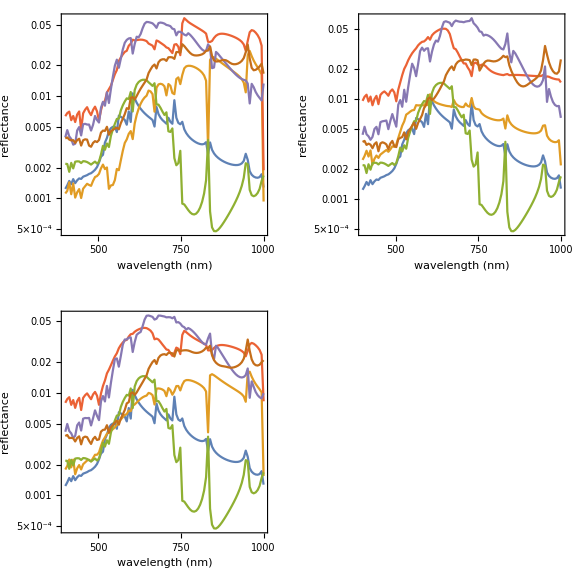

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorptance"},PlotRangePadding->None],{k,5,7}];
```

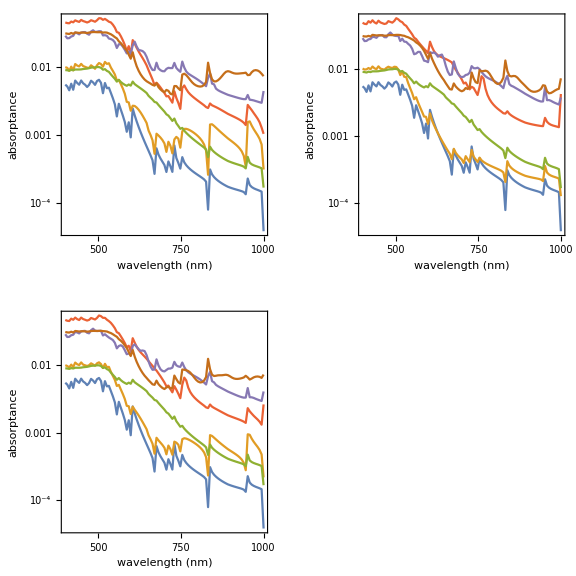

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance

```mathematica
g=Table[ListLogPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","transmittance"},PlotRangePadding->None],{k,8,10}];
```

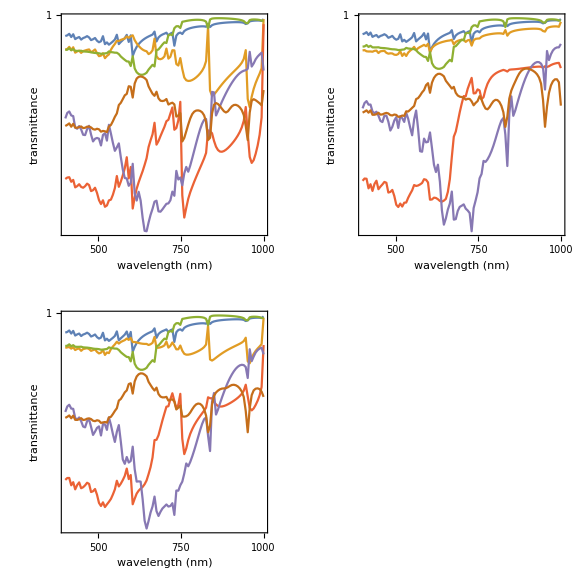

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{wav[[j]],data[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","absorbance"},PlotRangePadding->None],{k,8,10}];
```

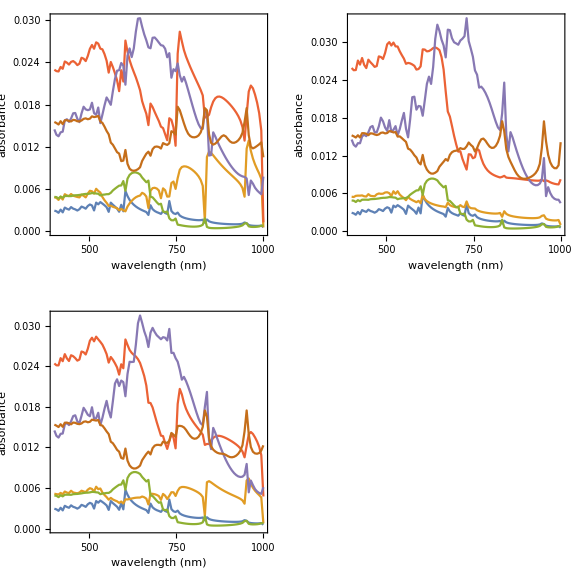

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Incident angle variation

```mathematica
vars={" incident alpha, beta"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"," unit cell reflectance"};
len={2,4,7,1,5,8,2,6,9,3};
datRS1=readmstm["pellucidus_ref_sphere.dat",vars,len];
datRS2H=readmstm["pellucidus_ref_bisphere_h.dat",vars,len];
datRS2V=readmstm["pellucidus_ref_bisphere_v.dat",vars,len];
datLC10H=readmstm["pellucidus_linear_chain_10_h.dat",vars,len];
datLC10V=readmstm["pellucidus_linear_chain_10_v.dat",vars,len];
datPC10=readmstm["pellucidus_packed_cluster_10.dat",vars,len];
dat={datRS1,datRS2H,datRS2V,datLC10H,datLC10V,datPC10};
```

### Reflectance

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","reflectance"},PlotRangePadding->None],{k,2,4}];
```

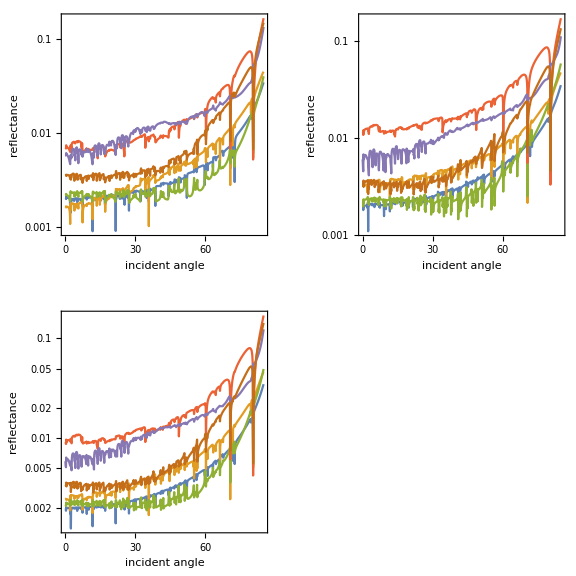

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorptance

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorptance"},PlotRangePadding->None],{k,5,7}];
```

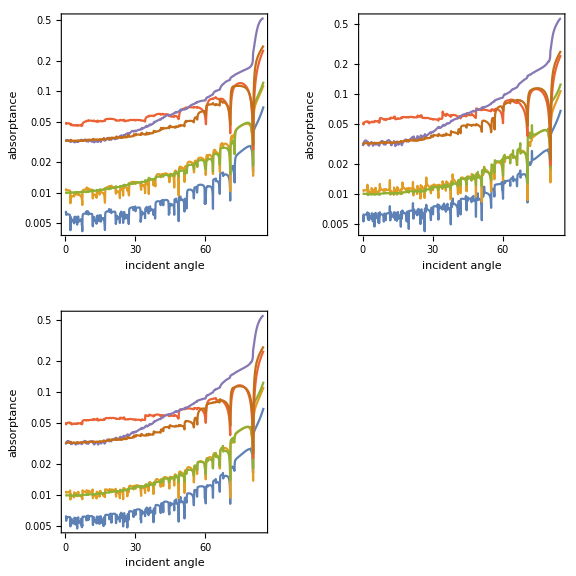

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Transmittance

```mathematica
g=Table[ListLogPlot[Table[{dat[[i,j,1]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","transmittance"},PlotRangePadding->None],{k,8,10}];
```

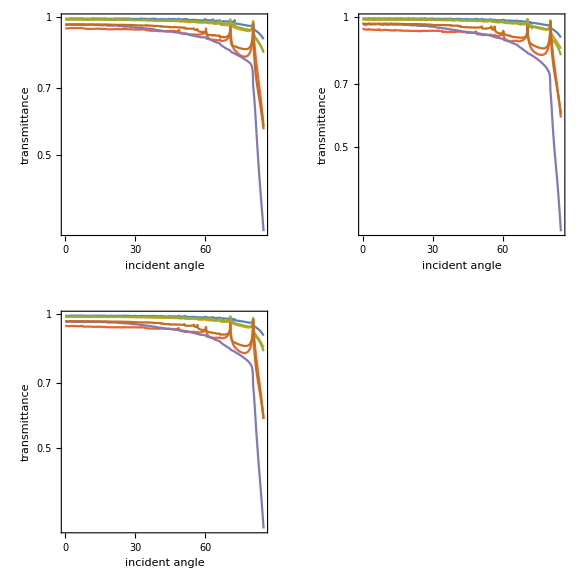

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

### Absorbance

```mathematica
data=dat;
Do[data[[All,All,i]]=-Log[10,dat[[All,All,i]]],{i,8,10}];
g=Table[ListPlot[Table[{dat[[i,j,1]],data[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[dat[[1]]]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"incident angle","absorbance"},PlotRangePadding->None],{k,8,10}];
```

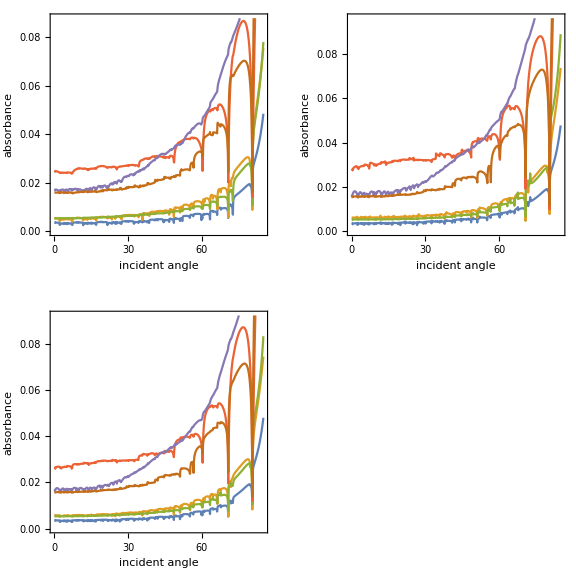

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single spheres","horizontal bispheres","vertical bispheres","horizontal linear chains of 10 spheres","vertical linear chains of 10 spheres","packed clusters of 10 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM